## 1D Atomic Chain

### Model

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

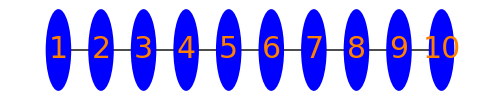

{{1,2},{2,1,3},{3,2,4},{4,3,5},{5,4,6},{6,5,7},{7,6,8},{8,7,9},{9,8,10},{10,9}}

```mathematica
dim=10;
t1=1.;t2=1.; (*t1=t2 for 1D simple chain*)
ϵ = Table[If[Mod[i,2]==0,t2,t1],{i,1,dim-1}]

s0 = Prepend[Table[{Sum[ϵ[[j]],{j,1,i}],0},{i,1,dim-1}],{0,0}];
model=Show[Graphics[{Black,Thick,Line[s0]}],Table[Graphics[{Blue,Ball[s0[[i]],0.3]}],{i,1,Length[s0]}]];
Show[model,Table[Graphics[Rotate[Text[ s0[[i]],s0[[i]]],π/6]],{i,1,Length[s0]}]];
Show[model,Table[Graphics[Rotate[Text[ Style[i,30,Orange],s0[[i]]],0]],{i,1,Length[s0]}],ImageSize->500]
sitepos = Table[If[i==1,{i,i+1},If[i==dim,{i,i-1},{i,i-1,i+1}]],{i,1,dim}]
site= Table[If[i==1,{s0[[i]],s0[[i+1]]},If[i==dim,{s0[[i]],s0[[i-1]]},{s0[[i]],s0[[i-1]],s0[[i+1]]}]],{i,1,dim}];
```

### Hamiltonian

```mathematica
(*spinless*)
ϵ1=0.;
Ham1 = Table[If[MemberQ[site[[r]],s0[[c]]],If[First[Flatten[Position[s0,s0[[c]]]]]==r ,ϵ1+1,If[First[Flatten[Position[s0,s0[[c]]]]]≠ r  ,Round[EuclideanDistance[s0[[r]],s0[[c]]],0.01] ,0]],0],{r,1,dim},{c,1,dim}];
Ham=Partition[Flatten[Ham1],dim];
Ham//MatrixForm//N
```

(1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 1. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 1. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 1. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1.)

### Two terminal Polarization

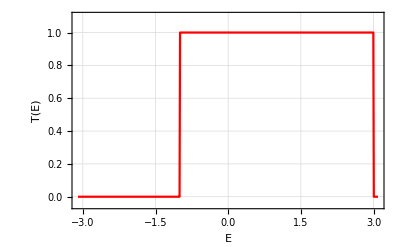

```mathematica
ϵ=0.;
t0=1.; τD=1;τS=1; 
ld1=1;ld2=dim;
leftE=-3.1;rightE=3.1;stepE=0.125/13;
Trans=ParallelTable[
En = DiagonalMatrix[Table[E1,{i,1,dim}]];
ΣS = Partition[Flatten[Table[If[a==ld1&&b==ld1,τS^2/(2 t0^2)((E1-ϵ-1)-ⅈ √(4 t0^2-(E1-ϵ-1)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣD =Partition[Flatten[Table[If[a==ld2 && b==ld2 ,τD^2/(2 t0^2)((E1-ϵ-1)-ⅈ √(4 t0^2-(E1-ϵ-1)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΓS=-2Im[ΣS];ΓD=-2Im[ΣD];
GR=Inverse[En-Ham-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,leftE,rightE,stepE}];

trup=ListLinePlot[Trans,PlotRange->{-0.05,1.1},Axes-> False,Frame->True,FrameStyle->Directive[Black,16],GridLines->Automatic,FrameLabel->{"E","T(E)"},PlotStyle->Directive[Red]]
```

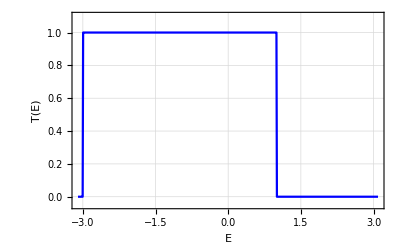

-Graphics-

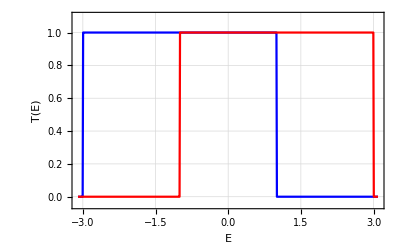

```mathematica
Show[%175,%174]
```

## Ladder

### Model

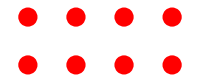

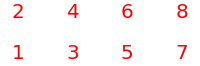

{{1,2,3},{2,1,4},{3,1,4,5},{4,2,3,6},{5,3,6,7},{6,4,5,8},{7,5,8},{8,6,7}}

```mathematica
dimx = 4; dimy=2; a=1;
unit = {{{0,0},{a,0},{a,a},{0,a}}};
latx = Table[unit[[1,i]]+k*{a,0},{k,0,dimx-2},{i,1,4}];
laty= Flatten[Table[latx[[j,i]]+k*{0,a},{j,1,Length[latx]},{k,1,dimy-2},{i,1,4}],1];
lat=Join[latx,laty];
model=Show[Table[Graphics[{EdgeForm[Thick],White,Polygon[lat[[i]]]}],{i,1,Length[lat]}],ImageSize->200];
s0=DeleteDuplicates[SortBy[Table[{Round[Flatten[lat,1][[i]][[1]],0.0001],Round[Flatten[lat,1][[i]][[2]],0.0001]},{i,1,Length[Flatten[lat,1]]}],First]]//Chop;
s0=s0*1.;
Show[model,Table[Graphics[{Red,Ball[s0[[i]],0.2]}],{i,1,Length[s0]}],ImageSize->200]
Show[model,Table[Graphics[Rotate[Text[ s0[[i]],s0[[i]]],π/6]],{i,1,Length[s0]}],ImageSize->200];
Show[model,Table[Graphics[Rotate[Text[ Style[i,20,Red],s0[[i]]],π/6]],{i,1,Length[s0]}],ImageSize->200]
lat1=Table[If[MemberQ[lat[[j]]*1.,s0[[i]]*1.],lat[[j]]*1.,##&[]],{i,1,Length[s0]},{j,1,Length[lat]}];
site=Table[Nearest[s0*1.,s0[[i]]*1.,{All,1}],{i,1,Length[s0]}];
sitepos=Table[First[Flatten[Position[s0*1.,site[[k,l]]*1.]]],{k,1,Length[site]},{l,1,Length[site[[k]]]}]
```

### Hamiltonian

```mathematica
(*spinless*)
ϵ1=0.;dim = Length[site];
Ham1 = Table[If[MemberQ[site[[r]],s0[[c]]],If[First[Flatten[Position[s0,s0[[c]]]]]==r ,ϵ1,If[First[Flatten[Position[s0,s0[[c]]]]]≠ r  ,Round[EuclideanDistance[s0[[r]],s0[[c]]],0.01] ,0]],0],{r,1,dim},{c,1,dim}];
Ham=Partition[Flatten[Ham1],dim];
Ham//MatrixForm//N
```

(0. | 1. | 1. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 1. | 1. | 0. | 0. | 0.
0. | 1. | 1. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 1. | 1. | 0.
0. | 0. | 0. | 1. | 1. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 0. | 1. | 1. | 0.)

### Two terminal Polarization

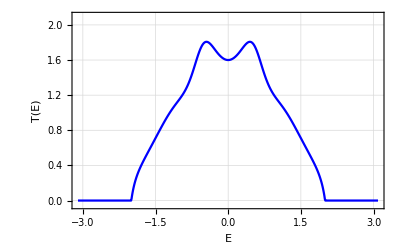

```mathematica
ϵ=0.;ΣS=.;
t0=1.; τD=1;τS=1; 
ld1=1;ld2=dim;
leftE=-3.1;rightE=3.1;stepE=0.125/13;
Trans=ParallelTable[
En = DiagonalMatrix[Table[E1,{i,1,dim}]];
ΣS1 = Partition[Flatten[Table[If[a==ld1&&b==ld1,τS^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣS2 = Partition[Flatten[Table[If[a==ld1+1&&b==ld1+1,τS^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣD1 =Partition[Flatten[Table[If[a==ld2-1 && b==ld2-1 ,τD^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣD2 =Partition[Flatten[Table[If[a==ld2 && b==ld2 ,τD^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣS=ΣS1+ΣS2;ΣD=ΣD1+ΣD2;
ΓS=-2Im[ΣS];ΓD=-2Im[ΣD];
GR=Inverse[En-Ham-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,leftE,rightE,stepE}];

trup=ListLinePlot[Trans,PlotRange->{-0.05,2.1},Axes-> False,Frame->True,FrameStyle->Directive[Black,16],GridLines->Automatic,FrameLabel->{"E","T(E)"},PlotStyle->Directive[Blue]]
```

```mathematica
ϵ=0.;ΣS=.;
t0=1.; τD=1;τS=1; 
ld1=1;ld2=dim;
leftE=-3.1;rightE=3.1;stepE=0.125/13;
En = DiagonalMatrix[Table[E1,{i,1,dim}]];
ΣS1 = Partition[Flatten[Table[If[a==ld1&&b==ld1,τS^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣS2 = Partition[Flatten[Table[If[a==ld1+1&&b==ld1+1,τS^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣD1 =Partition[Flatten[Table[If[a==ld2-1 && b==ld2-1 ,τD^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣD2 =Partition[Flatten[Table[If[a==ld2 && b==ld2 ,τD^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{a,1,dim},{b,1,dim}]],dim];
ΣS=ΣS1+ΣS2;ΣD=ΣD1+ΣD2;
ΣS//MatrixForm
```

(0.5 (0.+E1-ⅈ √(4.-(0.+E1)^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 (0.+E1-ⅈ √(4.-(0.+E1)^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)